```mathematica
<<"/home/denpak/Applications/Dynamica.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
gref=0.1
cap = 100
gpolt = 4.0 * gref
gpolh =0.01
epol = -70.0
gdep = 0.5 * gref
edep = 0.0
i = 0
gmin =0.2*gref
gmax=2.0*gref
vth =20.0
v0=2.0
gap = gmin + ((Gmax - gmin)/((1+Exp[(Vd-vth)/v0]) * (1+Exp[-(Vd+vth)/v0])))
```

These are the two differential equations combined into eq, I fix Vt to it’s equilibrium value which doesn’t change anything as far as I can tell because  
it’s internal polarity is orders of magnitude greater than the variation caused by the coupling to the other cell.

```mathematica
dvh = -gph*(Vh-epol)-gdep*(Vh-edep)-gap*(Vd)
dvt = -gpolt*(Vt-epol)-gdep*(Vt-edep)-gap*(-Vd)
eq =(dvh-dvt)/.{Vh->Vd+Vt}/.{Vt->-60}
```

-((0.02+(-0.02+Gmax)/((1+ⅇ^(0.5 (-20.-Vd))) (1+ⅇ^(0.5 (-20.+Vd))))) Vd)-0.05 (0.+Vh)-gph (70.+Vh)

(0.02+(-0.02+Gmax)/((1+ⅇ^(0.5 (-20.-Vd))) (1+ⅇ^(0.5 (-20.+Vd))))) Vd-0.05 (0.+Vt)-0.4 (70.+Vt)

1.-0.05 (-60.+Vd)-2 (0.02+(-0.02+Gmax)/((1+ⅇ^(0.5 (-20.-Vd))) (1+ⅇ^(0.5 (-20.+Vd))))) Vd-gph (10.+Vd)

```mathematica
Manipulate[Plot[(eq)/.{gph->gp,Gmax->gm},{Vd,0,80},PlotRange->{-5,5},AxesLabel->{"y","y/dt"}],{gp,0,0.04},{gm,0,0.2}]
```

```mathematica
ContourPlot3D[{eq==0},{Gmax,0,0.2},{gph,0,0.04},{Vd,0,50},RegionFunction->Function[{Gmax,gph,Vd},D[eq,Vd]>0]]
```

Syntax::bktmcp: Expression "ContourPlot3D[{eq==0},{Gmax,0,0.2},{gph,0,0.04},{Vd,0,50},RegionFunction→Function[{Gmax,gph,Vd},D[eq,Vd]>0]" has no closing "]".

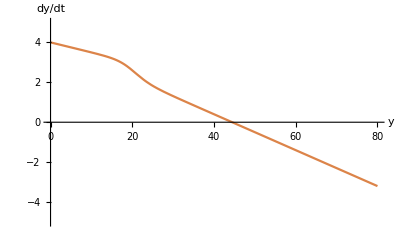
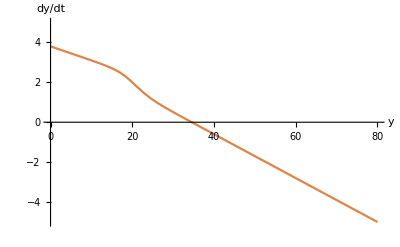
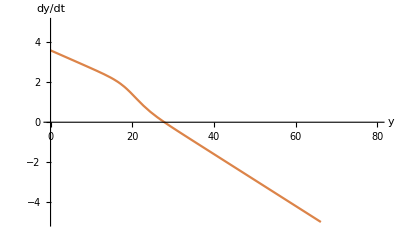
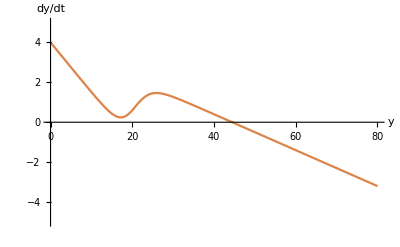
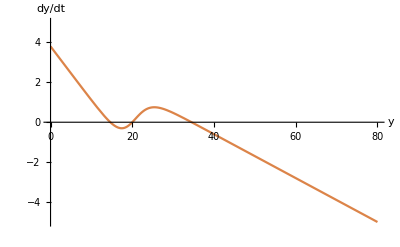
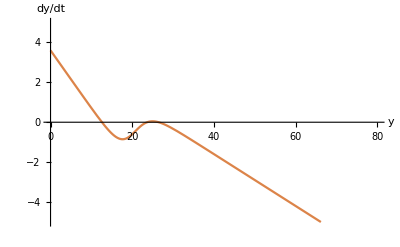
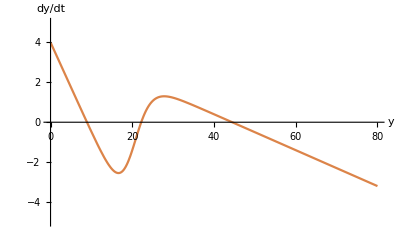
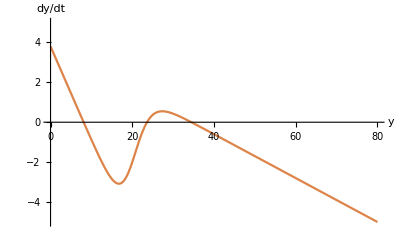

tmp.png

```mathematica
plots=Table[Plot[eq,{Vd,0,80},PlotStyle->RGBColor[220/255,132/255,73/255],AxesLabel->{"y","dy/dt"},PlotRange->{-5,5}],{Gmax,{0,0.1,0.2}},{gph,{0,0.02,0.04}}]
imgs=Transpose@plots;
g=Graphics[MapIndexed[Inset[#,#2]&,imgs,{2}],PlotRange->Thread[{1/4,2/3+Dimensions@imgs}],Axes->True,Ticks->{{{1,"0"},{2,"0.1"},{3,"0.2"}},{{1-0.05,"0"},{2-0.05,"0.02"},{3-0.05,"0.04"}}},AxesStyle->{{Thick,Arrowheads[0.03]},{Thick,Arrowheads[0.03]}},AxesOrigin->{1/4,1/4},ImageSize->700];
Export["tmp.png",Labeled[%,{"Head Cell Polarity","Maximal Gap Polarization"},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[Gray, Medium,FontFamily->"Helvetica",FontSize->15]]]
```